```mathematica
(* Guy F. Mongelli                                        ChE 400
Prof. Clark                                        11/16/2010  *)
```

```mathematica
(*Assignment #9 *)
```

```mathematica
(* Problem #1 *)
```

```mathematica
(*Part D *)
```

```mathematica
F[y_]:=1/(4 √π)NIntegrate[(2+k^2)Exp[-k^2/4]*Exp[-k*y],{k,0,∞}]
```

```mathematica
F[.5]
```

0.487518

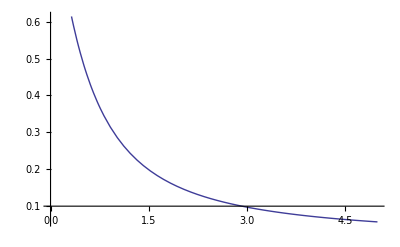

```mathematica
Plot[F[y],{y,0,5}]
```

```mathematica
(*Part E *)
```

```mathematica
Φ0=1;
a=1;
```

```mathematica
f[z_]:=Φ0*(1-(z/a)^2)*Exp[-(z/a)^2]
```

```mathematica
G[x_,y_]:=NIntegrate[f[z]/π*y/((x-z)^2+y^2),{z,-∞,∞}]
```

```mathematica
G[0,.5]
```

0.487518

```mathematica
Plot[G[0,y],{y,0,5}]
```

-Graphics-

```mathematica
(*Problem #3  *)
```

```mathematica
(*Problem #4 *)
```

```mathematica
DSolve[{y''[x]-2x*y'[x]+y[x]==0,y[0]==1,y'[0]==1},y[x],x]
```

{{y[x]→1/Gamma[1/4](√(2/π) Gamma[1/4] Gamma[3/4] HermiteH[1/2,x]+Gamma[1/4] Hypergeometric1F1[-1/4,1/2,x^2]-2 Gamma[3/4] Hypergeometric1F1[-1/4,1/2,x^2])}}

```mathematica
Series[1/Gamma[1/4](√(2/π) Gamma[1/4] Gamma[3/4] HermiteH[1/2,x]+Gamma[1/4] Hypergeometric1F1[-1/4,1/2,x^2]-2 Gamma[3/4] Hypergeometric1F1[-1/4,1/2,x^2]),{x,0,3}]
```

Power::infy: Infinite expression 1/0^1/4 encountered.

∞::indet: Indeterminate expression 0 x^2 ComplexInfinity Gamma[5/4]/√2 encountered.

Power::infy: Infinite expression 1/0^1/4 encountered.

∞::indet: Indeterminate expression 0 x^2 ComplexInfinity Gamma[5/4]/√2 encountered.

Indeterminate+x-(Gamma[3/4] x^2)/(4 Gamma[5/4])+(Gamma[3/4] x^3)/(8 Gamma[7/4])+O[x]^4

```mathematica
DSolve[{y''[x]-9*y[x]==0,y[0]==1,y'[0]==3},y[x],x]
```

{{y[x]→ⅇ^(3 x)}}

```mathematica
Series[ⅇ^(3 x),{x,0,10}]
```

1+3 x+(9 x^2)/2+(9 x^3)/2+(27 x^4)/8+(81 x^5)/40+(81 x^6)/80+(243 x^7)/560+(729 x^8)/4480+(243 x^9)/4480+(729 x^10)/44800+O[x]^11

```mathematica
DSolve[{x*y''[x]-y'[x]+x*y[x]==0,y[2]==1,y'[2]==-1},y[x],x]
```

{{y[x]→(x BesselJ[1,x] BesselY[0,2]+3 x BesselJ[1,x] BesselY[1,2]-x BesselJ[0,2] BesselY[1,x]-3 x BesselJ[1,2] BesselY[1,x]+x BesselJ[2,2] BesselY[1,x]-x BesselJ[1,x] BesselY[2,2])/(2 (BesselJ[1,2] BesselY[0,2]-BesselJ[0,2] BesselY[1,2]+BesselJ[2,2] BesselY[1,2]-BesselJ[1,2] BesselY[2,2]))}}

```mathematica
-(1/8)*(1-2*4)/6/5
```

7/240

```mathematica
81/40
```

81/40

```mathematica
27/8*9/5/6
```

81/80